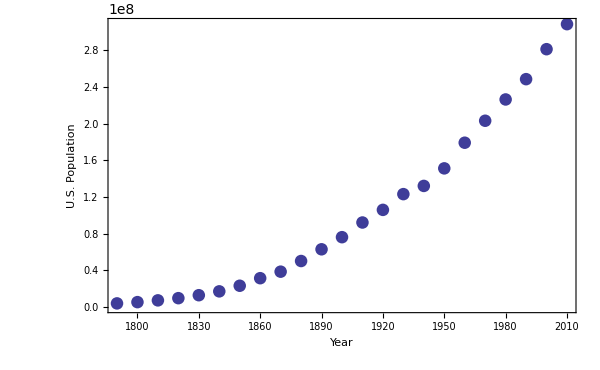

```mathematica
(*Data from http://www.census.gov/population/www/censusdata/files/table-2.pdf, http://www.census.gov/main/www/cen2000.html,http://quickfacts.census.gov/qfd/states/00000.html,retrieved February 15 2015 *) 
HistoricalPopulationDataUS = {
{1790,3929214},
{1800,5308438},
{1810,7239881},
{1820,9638453},
{1830,12866020},
{1840,17069453},
{1850,23191876},
{1860,31443321},
{1870,38558371},
{1880,50189209},
{1890,62979776},
{1900,76212168},
{1910,92228496},
{1920,106021537},
{1930,123202624},
{1940,132164569},
{1950,151325798},
{1960,179323175},
{1970,203302031},
{1980,226542199},
{1990,248709873},
{2000,281421906},
{2010,308745538}};

ListPlot[HistoricalPopulationDataUS,PlotStyle->PointSize[.015], Frame->True,FrameLabel->{"Year","U.S. Population","U.S. Population Data"},FrameStyle->Directive[FontSize-> 20],ImageSize->600]
```

```mathematica
Manipulate[Show[ListPlot[HistoricalPopulationDataUS,PlotStyle->PointSize[.015], Frame->True,FrameLabel->{"Year","U.S. Population","U.S. Population Data and Model for k="<>ToString[k]},FrameStyle->Directive[FontSize-> 20]],Plot[3929214Exp[k (x-1790)],{x,1790,2010},PlotStyle->{Thickness[0.005],ColorData[1,2]}],ImageSize->500],{k,.01,.04},LabelStyle-> Directive[FontSize->20]]
```

```mathematica
Manipulate[Show[ListPlot[HistoricalPopulationDataUS,PlotStyle->PointSize[.015], Frame->True,FrameLabel->{"Year","U.S. Population","U.S. Population Data and Model With Immigration for k="<>ToString[k] <> "and c="<>ToString[c]},FrameStyle->Directive[FontSize-> 20]],Plot[(-c+ⅇ^(k (-1790+t)) (c+3929214 k))/k,{t,1790,2010},PlotStyle->{Thickness[0.005],ColorData[1,2]}],ImageSize->600],{k,0.0001,.04},{c,0,900000},LabelStyle-> Directive[FontSize->20]]
```

```mathematica
Manipulate[Show[ListPlot[HistoricalPopulationDataUS,PlotStyle->PointSize[0.015],Frame->True,FrameLabel->{"Year","U.S. Population","U.S. Population Data with Exponential and Logistic Models"},FrameStyle->Directive[FontSize-> 20],
PlotLegends->PointLegend[{ColorData[1,1],ColorData[1,2],ColorData[1,3]},{"Historical Data                                                ","Exponential Model k =" <> ToString[k] ,"Logistic Model, M = "<>ToString[M/10^6] <>" million, r="<> ToString[r]},LegendMarkers->{{Graphics[{Disk[]}],15},{Graphics[{Line[{{0,0},{2,0}}]}],60},{Graphics[{Line[{{0,0},{2,0}}]}],60}},LegendFunction->"Frame",LabelStyle->20]],
Plot[3929214Exp[k (t-1790)],{t,1790,2010},PlotStyle->{ColorData[1,2],Thickness[0.005]}],
Plot[(3929214 ⅇ^(r (-1790+t)) M)/(-3929214+3929214 ⅇ^(r(-1790+t))+M) ,{t,1790,2010},PlotStyle->{Thickness[0.005],ColorData[1,3]}]
,ImageSize->550],{k,.01,.04},{M,300000000,800000000},{r,.01,.04},LabelStyle-> Directive[FontSize->20]]
```

```mathematica
(*Bacteria Culture: http://www.nature.com/srep/2014/140527/srep05057/full/srep05057.html, from Saikin,Semion K.,et al."Chromatic acclimation and population dynamics of green sulfur bacteria grown with spectrally tailored light." Scientific reports 4 (2014). *)
BacteriaData = {
{17.1633,0.1163},
{24.1732,0.168},
{37.9327,0.4231},
{49.9703,0.9121},
{62.0156,1.3378},
{74.0593,1.7762},
{89.7925,1.7151}
};
Manipulate[Show[ListPlot[BacteriaData,Frame-> True,PlotStyle->PointSize[0.015],FrameLabel->{"Time (Hours)","Density of Bacteria", "Experimental Bacteria Data and Logistic Model"},FrameStyle->Directive[FontSize-> 20],ImageSize->350,
PlotLegends->PointLegend[{ColorData[1,1],ColorData[1,3]},{"Bacteria Data                                 ","Logistic Model, M = "<>ToString[M] <>", r="<> ToString[r]},LegendMarkers->{{Graphics[{Disk[]}],15},{Graphics[{Line[{{0,0},{2,0}}]}],40},{Graphics[{Line[{{0,0},{2,0}}]}],40}},LegendFunction->"Frame",LabelStyle->20]],Plot[(0.02 ⅇ^(r t) M)/(0.02(-1+ⅇ^(r t))+M) ,{t,0,90},PlotStyle->{Thickness[0.005],ColorData[1,3]}]],{M,1,3},{r,.05,.3},LabelStyle-> Directive[FontSize->20]]
```

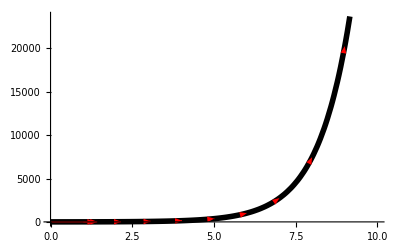

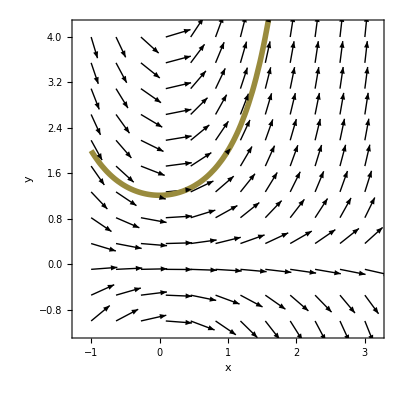

```mathematica
DirectionField[f_,xrange_,yrange_]:=VectorPlot[{1/(√(1+f^2)),f/(√(1+f^2))},xrange,yrange,VectorPoints->12,VectorScale->Small,VectorStyle->Black,Frame->True,FrameLabel->{"x","y"},FrameStyle->Directive[FontSize-> 20],RotateLabel->False]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
DirectionFieldWithSolutions[f_,InitialData_,xrange_,yrange_,xmax_]:=Module[{init,sol,kk,result},
result = DirectionField[f,xrange,yrange];
For[kk=1,kk≤ Length[InitialData],kk++,
sol= NDSolve[{y'[x]==(f/.y->y[x]),y[InitialData[[kk,1]]]==InitialData[[kk,2]]},y[x],{x,InitialData[[kk,1]],xmax}];
result =Show[result,Plot[y[x]/.sol,{x,InitialData[[kk,1]],xmax},PlotStyle->{ColorData[1,kk+1],Thickness[0.01]}]];
];
result
]

SingleArrow[p_,q_,f_,len_]:=Graphics[{Red,Thick,Arrow[{{p,q},{p+len/(√(1 +(f/.{x->p,y->q})^2)),q+(len(f/.{x->p,y->q}))/(√(1 +(f/.{x->p,y->q})^2))}}]}]
DirectionFieldAlongSolutionCurve[f_,xmin_,xmax_,init_,numarrows_,len_]:=Module[{sol,kk, result,arrowlocs},
sol =  NDSolve[{y'[x]==(f/.y->y[x]),y[xmin]==init},y[x],{x,xmin,xmax}];
result = Plot[y[x]/.sol,{x,xmin,xmax},PlotStyle-> {Black,Thickness[0.01]}];
arrowlocs=({x,y[x]}/. sol[[1]]/.x->#)&/@ (((xmax-xmin)Range[0,numarrows])/numarrows)+xmin;
For[kk=1,kk≤numarrows,kk++,
result=Show[result,SingleArrow[arrowlocs[[kk,1]],arrowlocs[[kk,2]],f,len]]
];
result
]
DirectionFieldAlongSolutionCurve[y + Sin[x],0,10,2,10,3]
DirectionFieldWithSolutions[x y,{{0,1},{-1,2},{1,-1}},{x,-1,3},{y,-1,4},10]
```

```mathematica
?Arrow
```

RowBox[{"Arrow", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["pt", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["pt", "TI"], StyleBox["2", "TR"]]}], "}"}], "]"}] is a graphics primitive that represents an arrow from SubscriptBox[StyleBox["pt", "TI"], StyleBox["1", "TR"]] to SubscriptBox[StyleBox["pt", "TI"], StyleBox["2", "TR"]].
RowBox[{"Arrow", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["pt", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["pt", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["s", "TI"]}], "]"}] represents an arrow with its ends set back from SubscriptBox[StyleBox["pt", "TI"], StyleBox["1", "TR"]] and SubscriptBox[StyleBox["pt", "TI"], StyleBox["2", "TR"]] by a distance StyleBox["s", "TI"]. 
RowBox[{"Arrow", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["pt", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["pt", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["s", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["s", "TI"], StyleBox["2", "TR"]]}], "}"}]}], "]"}] sets back by SubscriptBox[StyleBox["s", "TI"], StyleBox["1", "TR"]] from SubscriptBox[StyleBox["pt", "TI"], StyleBox["1", "TR"]] and SubscriptBox[StyleBox["s", "TI"], StyleBox["2", "TR"]] from SubscriptBox[StyleBox["pt", "TI"], StyleBox["2", "TR"]]. 
RowBox[{"Arrow", "[", RowBox[{StyleBox["curve", "TI"], ",", StyleBox["…", "TR"]}], "]"}] represents an arrow following the specified StyleBox["curve", "TI"].

```mathematica
DirectionField[f_,xrange_,yrange_]:=VectorPlot[{1/(√(1+f^2)),f/(√(1+f^2))},xrange,yrange,VectorPoints->12,VectorScale->Small,VectorStyle->Black,Frame->True,FrameLabel->{"x","y"," "," "},FrameStyle->Directive[FontSize-> 20],RotateLabel->False]/.Arrow[{p_,q_}]:>Arrow[{p+(q-p)/2,q+(q-p)/2}]
Export["simple_slope_field.pdf",Show[DirectionField[y(1-y/10),{x,0,20},{y,-3,21}],ImageSize->300]]
```

simple_slope_field.pdf